## Import Utils

```mathematica
Get["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
(*NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]*)
```

```mathematica
NotebookEvaluate["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"]
```

输入Mc范围：{8,15}

输入q范围：{1,20}

m1范围：{9.18959,91.4002}

m2范围：{2.43734,17.2305}

输入Mc范围：{6,13}

输入q范围：{1,7}

m1范围：{6.89219,42.9142}

m2范围：{2.8295,14.9331}

全局极小值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极大值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{2.81559×10^-11,{m1→46.8969,m2→60.4341,spin1z→0.435746,spin2z→-0.638885}}

全局极大值结果：{8.65708,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{8.47209×10^-10,{m1→60.1419,m2→76.87,spin1z→0.320417,spin2z→-0.443897}}

全局极大值结果：{1.94773,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

## 设置non-GR参数字符flag Gw@150914!

```mathematica
eventID="GW170104";

deviationType="cpsi";
deviationOrders=List[0,2,3,4,"5l",6,"6l"];
deviationNames=List["cpsi0","cpsi2","cpsi3","cpsi4","cpsi5l","cpsi6","cpsi6l"];
psiNames=List["psi0","psi2","psi3","psi4","psi5l","psi6","psi6l"];

deviationType="cpsi";
deviationOrders=List[0,2,3,4,"5l",6,"6l",7];
deviationNames=List["cpsi0","cpsi2","cpsi3","cpsi4","cpsi5l","cpsi6","cpsi6l","cpsi7"];
psiNames=List["psi0","psi2","psi3","psi4","psi5l","psi6","psi6l","psi7"];
```

```mathematica
csvPath="D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv"<>"\\"<>eventID;
csvNames=eventID<>"_"<>#<>".csv"& /@ deviationNames;

csvFilePaths=csvPath<>"\\"<>#& /@ csvNames;
```

### from CSV

```mathematica
samples=<||>;
Do[
CSVSamples=Import["D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv\\"<>eventID<>"\\"<>eventID<>"_"<>n<>".csv"];
samples[n]=<||>;
samples[n]["mass1"]=CSVSamples[[All,1]][[2;;]];
samples[n]["mass2"]=CSVSamples[[All,2]][[2;;]];
samples[n]["spin1z"]=CSVSamples[[All,3]][[2;;]];
samples[n]["spin2z"]=CSVSamples[[All,4]][[2;;]];
samples[n]["eta"]=CSVSamples[[All,5]][[2;;]];
samples[n]["Mchirp"]=CSVSamples[[All,6]][[2;;]];
samples[n][n]=CSVSamples[[All,7]][[2;;]];
samples[n]["chis"]=χs[samples["spin1z"],samples["spin2z"]];
samples[n]["chia"]=χa[samples["spin1z"],samples["spin2z"]];,
{n,deviationNames}
]
```

### Calculate GR Coefficients

```mathematica
Do[
samples[deviationNames[[n]]][psiNames[[n]]]=MapThread[
Psi[deviationOrders[[n]],η[#1,#2],M[#1,#2],#3,#4]&,
{samples[deviationNames[[n]]]["mass1"],samples[deviationNames[[n]]]["mass2"],samples[deviationNames[[n]]]["spin1z"],samples[deviationNames[[n]]]["spin2z"]}
];,
{n,Range[Length[deviationOrders]]}
]
```

### Calculate BCIs

```mathematica
BCI=<||>;
Do[
BCI[deviationNames[[n]]]=<||>;
BCI[deviationNames[[n]]]["mass1"]=PlotParameterWithBCI[samples[deviationNames[[n]]]["mass1"],Subscript["m","1"]][[1]];
BCI[deviationNames[[n]]]["mass2"]=PlotParameterWithBCI[samples[deviationNames[[n]]]["mass2"],Subscript["m","2"]][[1]];
BCI[deviationNames[[n]]]["spin1z"]=PlotParameterWithBCI[samples[deviationNames[[n]]]["spin1z"],"spin1z"][[1]];
BCI[deviationNames[[n]]]["spin2z"]=PlotParameterWithBCI[samples[deviationNames[[n]]]["spin2z"],"spin2z"][[1]];
BCI[deviationNames[[n]]][deviationNames[[n]]]=PlotParameterWithBCI[samples[deviationNames[[n]]][deviationNames[[n]]],deviationNames[[n]]][[1]];
BCI[deviationNames[[n]]][psiNames[[n]]]=PlotParameterWithBCI[samples[deviationNames[[n]]][psiNames[[n]]],psiNames[[n]]][[1]];,
{n,Range[Length[deviationOrders]]}
]
```

```mathematica
widths={};
Do[
AppendTo[widths,(BCI[deviationNames[[n]]][deviationNames[[n]]][[3]]-BCI[deviationNames[[n]]][deviationNames[[n]]][[1]])/(BCI[deviationNames[[n]]][psiNames[[n]]][[3]]-BCI[deviationNames[[n]]][psiNames[[n]]][[1]])],
{n,Range[Length[deviationOrders]]}
];
Round[widths,0.0001]
widths={};
Do[
AppendTo[widths,BCI[deviationNames[[n]]][deviationNames[[n]]][[3]]-BCI[deviationNames[[n]]][deviationNames[[n]]][[1]]],
{n,Range[Length[deviationOrders]]}
];
Round[widths/{5000,250,150,5,1.5,0.5,0.1},0.0001]
```

{0.1967,1.5019,41.3175,45.9703,3.5902,7.1967,43.4189,10.6121}

Thread::tdlen: Objects of unequal length in {1055.45,302.117,10219.1,269.065,40.2385,54.9113,9.37476,15.1091} {1/5000,1/250,1/150,1/5,0.666667,2.,10.} cannot be combined.

Round[{1/5000,1/250,1/150,1/5,0.666667,2.,10.} {1055.45,302.117,10219.1,269.065,40.2385,54.9113,9.37476,15.1091},0.0001]

```mathematica
o="5l";
{Quantile[samples["cpsi"<>o]["psi"<>o],{0.05,0.95}]-Median[samples["cpsi"<>o]["psi"<>o]],Median[samples["cpsi"<>o]["psi"<>o]]}
```

{{-5.38601,5.8217},17.2731}

```mathematica
medians={};
Do[
AppendTo[medians,BCI[deviationNames[[n]]][deviationNames[[n]]][[2]]/BCI[deviationNames[[n]]][psiNames[[n]]][[2]]],
{n,Range[Length[deviationOrders]]}
];
Round[medians,0.0001]
```

{0.7424,2.5322,13.3264,15.6135,-4.3244,16.7808,18.3346,-2.387}

## m1-m2 Plot, 22

```mathematica
pInterval=<||>;
tapeIntervals=<||>;
tapes=<||>;
plots=<||>;
compPlots=<||>;
lines=<||>;
legends=<||>;

m1m2=<||>;
m1PriorRange=<||>;
m2PriorRange=<||>;
m1m2PDF=<||>;
contourPD=<||>;
contourPlotObj=<||>;
contourPoints=<||>;
smoothedContourPoints=<||>;
```

```mathematica
BCI
```

<|cpsi0→<|mass1→{27.8001,45.4635,56.164},mass2→{7.5888,11.0762,19.285},spin1z→{0.0669802,0.570596,0.83343},spin2z→{-0.859887,0.231708,0.898089},cpsi0→{15657.4,18325.4,19360.},psi0→{14939.4,18206.3,27807.}|>,cpsi2→<|mass1→{22.5562,38.5337,58.7621},mass2→{7.87779,12.3079,17.9034},spin1z→{-0.0115364,0.533351,0.84644},spin2z→{-0.893286,-0.241835,0.593196},cpsi2→{1920.93,2483.56,3155.07},psi2→{898.156,996.398,1302.55}|>,cpsi6l→<|mass1→{26.1185,40.2256,52.8701},mass2→{9.96719,13.5835,19.7334},spin1z→{0.125456,0.618524,0.874937},spin2z→{-0.902033,-0.438706,0.480844},cpsi6l→{-23.3249,-19.0778,-12.9436},psi6l→{-1.83024,-1.26922,-0.933476}|>|>

### 0/2PN

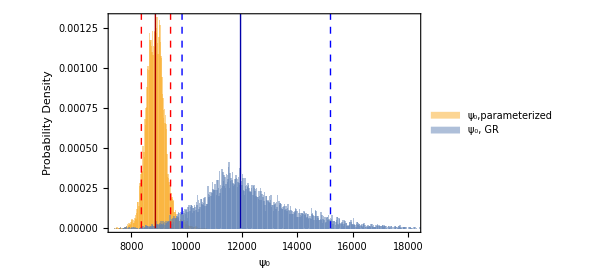

输入Mc范围：{11,22}

输入q范围：{1,12}

m1范围：{12.6357,99.285}

m2范围：{4.13688,25.2714}

原始数据量 = 46745，降采样后数据量 = 46745（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在有限先验区间内的积分值S = 0.584804

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 3.37657×10^-6 for the integral and error estimates.

归一化后先验区间内积分值 = 1.（误差应<1e-5）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{0.0008}

等高线数量：1 条

第一条等高线的前5个边界点：{{24.3378,25.0148},{23.8161,24.894},{23.7389,24.8276},{22.5204,24.5166},{23.6556,24.1852}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

===== 第i$172970条等高线 =====

包含闭合区域数：1

区域内总积分值：0.907105

可信水平百分比：90.7105%

==========================

{{41.6081,25.0129},{41.6036,24.9991},{41.3983,24.894},{41.5659,24.7796},{42.04,24.5166},{41.6966,24.2216},{41.8009,24.0822},{42.0346,23.8338},{42.1699,23.7618},{42.5969,23.5215},{43.1171,23.1203},{43.2547,23.007},{43.2126,22.9169},{43.5819,22.762},{43.9256,22.6296},{43.7823,22.301},{43.8386,22.2522},{43.763,22.208},{43.5819,22.1872},{42.0396,21.8747},{42.0362,21.8744},{42.0346,21.87},{42.0045,21.4973},{42.0346,21.4519},{42.622,21.2632},{42.716,20.9537},{43.0694,20.7425},{43.2108,20.652},{43.5819,20.0533},{43.6797,19.9877},{43.6673,19.9669},{43.5819,19.6034},{43.5445,19.2421},{43.5489,19.2329},{43.5538,19.2261},{43.5767,18.8555},{43.5819,18.7439},{43.6128,18.4857},{43.6068,18.4781},{43.6081,18.4717},{43.6415,17.7379},{43.6463,17.7233},{43.6471,17.7074},{43.5819,17.6099},{42.5977,17.3459},{42.2625,17.2903},{41.6476,17.2516},{40.4873,17.2045},{39.441,17.4681},{38.8141,17.3766},{38.5403,17.3459},{37.3926,17.1322},{37.1629,17.0246},{37.0116,16.9685},{36.6574,16.7892},{36.2654,16.4887},{34.5498,16.2751},{34.298,16.2329},{34.1282,16.2551},{31.4003,16.2618},{31.2034,16.2438},{29.8472,16.5911},{29.7439,16.6126},{29.6561,16.6582},{28.9897,16.9685},{28.6304,17.0958},{28.3783,17.6576},{28.3068,17.7233},{28.2638,17.7612},{28.1088,18.0737},{28.0767,18.1007},{27.6893,18.3758},{27.394,18.4781},{27.479,18.6317},{27.1047,18.988},{27.0038,19.2329},{26.9252,19.5216},{26.7857,19.665},{26.1461,19.9877},{26.5624,20.3649},{26.5618,20.3652},{26.5615,20.3657},{25.5385,20.7425},{25.2625,20.8031},{25.0142,20.9748},{24.744,21.1199},{24.3067,21.3248},{24.266,21.4973},{24.2377,21.6867},{23.8697,21.973},{23.8446,22.2522},{23.8173,22.5441},{23.6829,22.6823},{22.6194,23.007},{23.6635,23.3364},{23.632,23.4246},{23.6483,23.7618},{23.6791,24.0874},{23.7374,24.2051},{22.6706,24.5166},{23.8157,24.8089},{23.9147,24.894},{24.4707,25.0148},{41.6081,25.0129}}

```mathematica
order=0;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[{11,22},{1,12}];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.0008};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];
```

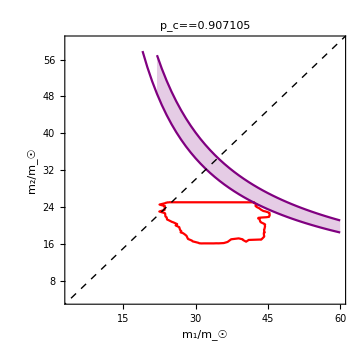

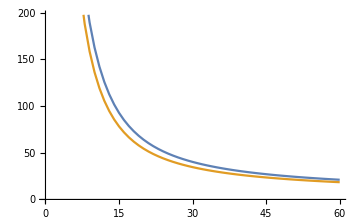

```mathematica
m1s=Range[4,60,1];
m2s=Range[4,60,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
Append[contourPoints[n][[1]],contourPoints[n][[1]][[1]]],

Select[tapes[n][n][[1]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]],
Select[tapes[n][n][[2]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]

ListLinePlot[{tapes[n][n][[1]][[2;;]],tapes[n][n][[2]][[2;;]]}]
```

### 2/2PN

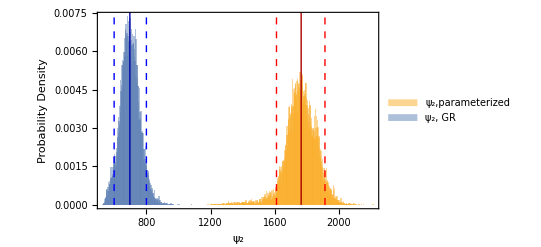

输入Mc范围：{16,33}

输入q范围：{1,7}

m1范围：{18.3792,108.936}

m2范围：{7.54535,37.907}

原始数据量 = 47989，降采样后数据量 = 47989（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在有限先验区间内的积分值S = 1.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.999999 and 9.02096×10^-6 for the integral and error estimates.

归一化后先验区间内积分值 = 0.999999（误差应<1e-5）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{1.×10^-6}

等高线数量：1 条

第一条等高线的前5个边界点：{{38.0111,37.6176},{38.4117,37.5753},{38.5927,37.4336},{38.7608,37.3649},{39.1138,37.2685}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

===== 第i$203665条等高线 =====

包含闭合区域数：1

区域内总积分值：0.999988

可信水平百分比：99.9988%

==========================

```mathematica
order=2;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[{16,33},{1,7}];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.000001};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];
```

0.9999

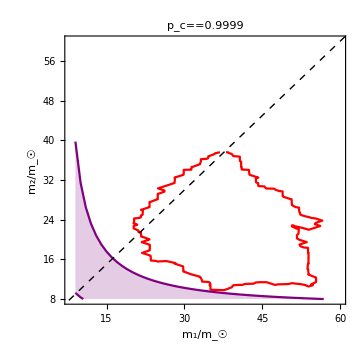

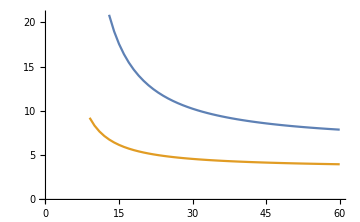

```mathematica
(*prob=0.3*)
m1s=Range[8,60,1];
m2s=Range[8,60,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]

ListLinePlot[{tapes[n][n][[1]][[2;;]],tapes[n][n][[2]][[2;;]]}]
```

```mathematica
contourPoints[n]
```

{{{26.6694,18.2442},{26.9285,18.117},{27.3117,17.9143},{27.7305,17.5021},{27.7369,17.4961},{27.75,17.4838},{28.2861,17.1351},{29.0799,16.7824},{29.6289,16.5262},{31.5282,16.3701},{31.7397,16.3558},{31.8925,16.3431},{32.3437,16.2724},{33.0696,16.2103},{33.99,16.0831},{34.3995,15.9537},{35.4884,15.6575},{35.6645,15.6275},{35.994,15.5352},{37.0593,15.3253},{37.5313,15.2609},{38.0134,15.0427},{38.2656,14.9855},{38.3892,14.9626},{39.2292,14.8162},{39.7191,14.6304},{40.4103,14.4278},{40.8646,14.3426},{41.049,14.2962},{41.5942,14.1757},{41.7139,14.1546},{41.7723,14.1474},{41.8769,14.1204},{42.2248,14.0609}}}

### 3/2PN

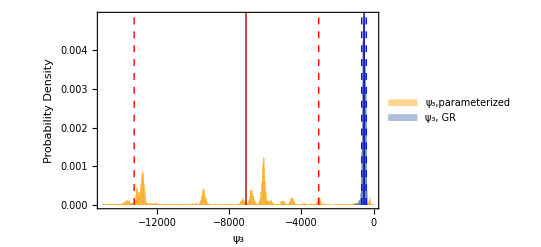

输入Mc范围：{16,33}

输入q范围：{1,7}

m1范围：{18.3792,108.936}

m2范围：{7.54535,37.907}

原始数据量 = 50004，降采样后数据量 = 50004（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在有限先验区间内的积分值S = 1.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.999999 and 7.87001×10^-6 for the integral and error estimates.

归一化后先验区间内积分值 = 0.999999（误差应<1e-5）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{1.×10^-6}

等高线数量：5 条

第一条等高线的前5个边界点：{{50.9614,9.71404},{52.6788,9.0576},{52.7147,8.62969},{53.3189,8.41642},{53.955,8.31677}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

General::stop: Further output of NIntegrate::regm will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

===== 第i$164194条等高线 =====

包含闭合区域数：5

区域内总积分值：0.999972

可信水平百分比：99.9972%

==========================

```mathematica
order=3;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[{16,33},{1,7}];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.000001};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];
```

0.9999

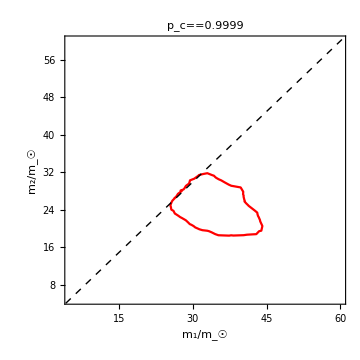

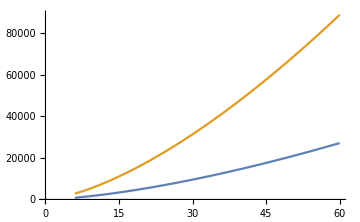

```mathematica
prob=0.9999
m1s=Range[5,60,1];
m2s=Range[5,60,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]

ListLinePlot[{tapes[n][n][[1]][[2;;]],tapes[n][n][[2]][[2;;]]}]
```

```mathematica
tapes[n][n][[1]][[2;;]]
```

{{6,832.989},{7,1053.14},{8,1290.09},{9,1542.75},{10,1810.22},{11,2091.72},{12,2386.62},{13,2694.33},{14,3014.36},{15,3346.26},{16,3689.61},{17,4044.06},{18,4409.28},{19,4784.97},{20,5170.83},{21,5566.63},{22,5972.1},{23,6387.05},{24,6811.24},{25,7244.5},{26,7686.63},{27,8137.47},{28,8596.85},{29,9064.62},{30,9540.63},{31,10024.7},{32,10516.8},{33,11016.8},{34,11524.4},{35,12039.7},{36,12562.5},{37,13092.6},{38,13630.1},{39,14174.7},{40,14726.5},{41,15285.3},{42,15851.},{43,16423.6},{44,17002.9},{45,17589.},{46,18181.6},{47,18780.8},{48,19386.4},{49,19998.5},{50,20616.9},{51,21241.6},{52,21872.5},{53,22509.5},{54,23152.7},{55,23801.9},{56,24457.1},{57,25118.2},{58,25785.1},{59,26457.9},{60,27136.5}}

### 4/2PN

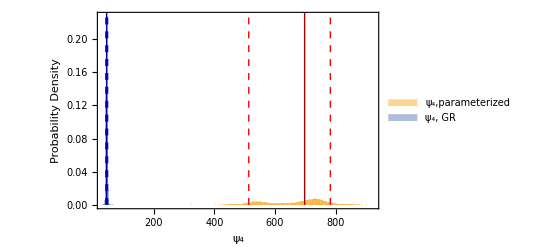

输入Mc范围：{16,33}

输入q范围：{1,7}

m1范围：{18.3792,108.936}

m2范围：{7.54535,37.907}

原始数据量 = 47986，降采样后数据量 = 47986（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在有限先验区间内的积分值S = 1.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.999999 and 7.23039×10^-6 for the integral and error estimates.

归一化后先验区间内积分值 = 0.999999（误差应<1e-5）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{0.002}

等高线数量：1 条

第一条等高线的前5个边界点：{{27.9297,22.184},{27.3804,22.4911},{27.0771,22.7262},{26.4646,23.1456},{26.3276,23.2224}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

===== 第i$230709条等高线 =====

包含闭合区域数：1

区域内总积分值：0.854856

可信水平百分比：85.4856%

==========================

```mathematica
order=4;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[{16,33},{1,7}];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.002};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[-1]][[2]];
```

0.85

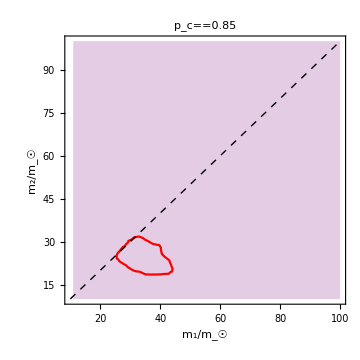

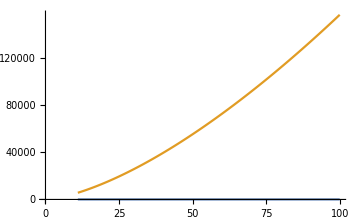

```mathematica
prob=0.85
m1s=Range[10,100,1];
m2s=Range[10,100,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]

ListLinePlot[{tapes[n][n][[1]][[2;;]],tapes[n][n][[2]][[2;;]]}]
```

```mathematica
tapes[n][n][[1]][[2;;]]
```

{{11,3226.4},{12,3679.48},{13,4152.11},{14,4643.52},{15,5153.04},{16,5680.04},{17,6223.97},{18,6784.32},{19,7360.64},{20,7952.49},{21,8559.48},{22,9181.25},{23,9817.45},{24,10467.8},{25,11131.9},{26,11809.6},{27,12500.6},{28,13204.6},{29,13921.4},{30,14650.7},{31,15392.5},{32,16146.3},{33,16912.2},{34,17689.8},{35,18479.1},{36,19279.8},{37,20091.8},{38,20914.9},{39,21749.},{40,22593.9},{41,23449.6},{42,24315.8},{43,25192.5},{44,26079.5},{45,26976.7},{46,27883.9},{47,28801.2},{48,29728.4},{49,30665.3},{50,31611.9},{51,32568.1},{52,33533.7},{53,34508.7},{54,35493.1},{55,36486.6},{56,37489.3},{57,38501.},{58,39521.7},{59,40551.3},{60,41589.7},{61,42636.9},{62,43692.7},{63,44757.1},{64,45830.},{65,46911.4},{66,48001.2},{67,49099.4},{68,50205.8},{69,51320.4},{70,52443.1},{71,53574.},{72,54712.9},{73,55859.8},{74,57014.6},{75,58177.2},{76,59347.7},{77,60526.},{78,61711.9},{79,62905.6},{80,64106.8},{81,65315.6},{82,66532.},{83,67755.8},{84,68987.},{85,70225.7},{86,71471.6},{87,72724.9},{88,73985.5},{89,75253.2},{90,76528.1},{91,77810.2},{92,79099.4},{93,80395.6},{94,81698.8},{95,83009.1},{96,84326.3},{97,85650.3},{98,86981.3},{99,88319.1},{100,89663.7}}

### 5/2PN, log

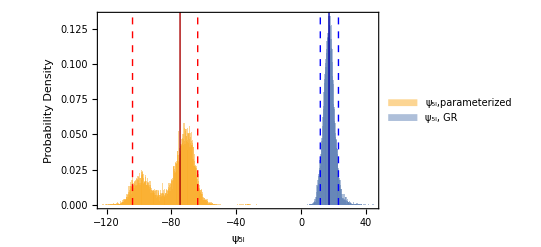

输入Mc范围：{16,33}

输入q范围：{1,7}

m1范围：{18.3792,108.936}

m2范围：{7.54535,37.907}

原始数据量 = 48859，降采样后数据量 = 48859（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在有限先验区间内的积分值S = 1.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 9.127×10^-6 for the integral and error estimates.

归一化后先验区间内积分值 = 1.（误差应<1e-5）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{1.×10^-6}

等高线数量：1 条

第一条等高线的前5个边界点：{{40.8931,11.8407},{40.7406,10.8915},{40.3914,10.7984},{39.4013,10.3379},{39.3339,10.2788}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

===== 第i$186575条等高线 =====

包含闭合区域数：1

区域内总积分值：0.999975

可信水平百分比：99.9975%

==========================

```mathematica
order="5l";
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[{16,33},{1,7}];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.000001};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];
```

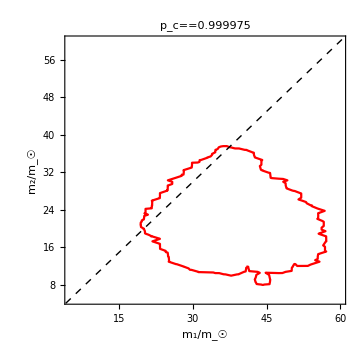

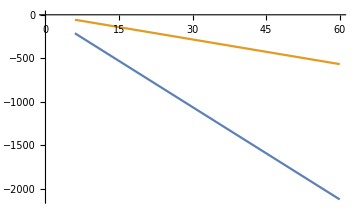

```mathematica
m1s=Range[5,60,1];
m2s=Range[5,60,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

Reverse/@tapes[n][n][[1]][[2;;]],
Reverse/@tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]

ListLinePlot[{tapes[n][n][[1]][[2;;]],tapes[n][n][[2]][[2;;]]}]
```

### 6/2PN; no solution

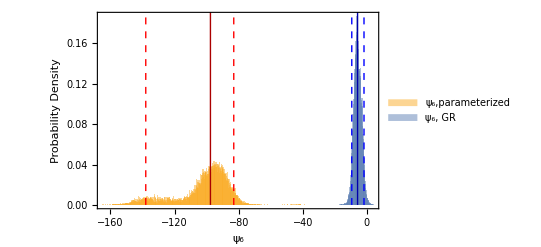

输入Mc范围：{16,33}

输入q范围：{1,7}

m1范围：{18.3792,108.936}

m2范围：{7.54535,37.907}

原始数据量 = 46761，降采样后数据量 = 46761（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在有限先验区间内的积分值S = 1.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.999999 and 8.87145×10^-6 for the integral and error estimates.

归一化后先验区间内积分值 = 0.999999（误差应<1e-5）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{1.×10^-6}

等高线数量：1 条

第一条等高线的前5个边界点：{{39.8766,11.3406},{41.0184,11.3873},{42.4183,11.4134},{42.6354,11.6433},{43.4337,11.8827}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

===== 第i$195780条等高线 =====

包含闭合区域数：1

区域内总积分值：0.99999

可信水平百分比：99.999%

==========================

```mathematica
order=6;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[{16,33},{1,7}];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.000001};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];
```

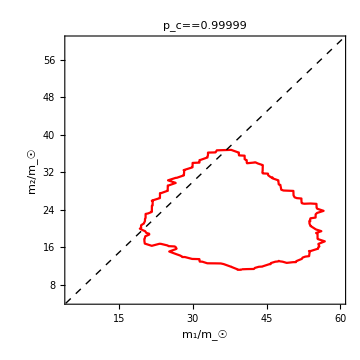

-Graphics-

```mathematica
m1s=Range[5,60,1];
m2s=Range[5,60,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]

ListLinePlot[{tapes[n][n][[1]][[2;;]],tapes[n][n][[2]][[2;;]]}]
```

```mathematica
tapes[n][n][[2]][[2;;]]
```

{{6,181.289},{7,195.811},{8,209.338},{9,222.043},{10,234.052},{11,245.462},{12,256.349},{13,266.774},{14,276.786},{15,286.427},{16,295.731},{17,304.727},{18,313.44},{19,321.893},{20,330.105},{21,338.092},{22,345.87},{23,353.451},{24,360.848},{25,368.072},{26,375.131},{27,382.035},{28,388.793},{29,395.41},{30,401.894},{31,408.252},{32,414.488},{33,420.609},{34,426.618},{35,432.521},{36,438.322},{37,444.025},{38,449.633},{39,455.15},{40,460.58},{41,465.925},{42,471.188},{43,476.371},{44,481.479},{45,486.512},{46,491.473},{47,496.365},{48,501.189},{49,505.947},{50,510.642},{51,515.275},{52,519.847},{53,524.361},{54,528.818},{55,533.218},{56,537.565},{57,541.859},{58,546.101},{59,550.293},{60,554.436},{61,558.53},{62,562.578},{63,566.579},{64,570.536},{65,574.449},{66,578.319},{67,582.147},{68,585.934},{69,589.68},{70,593.387},{71,597.055},{72,600.684},{73,604.277},{74,607.833},{75,611.354},{76,614.839},{77,618.289},{78,621.705},{79,625.089},{80,628.439},{81,631.757},{82,635.043},{83,638.299},{84,641.524},{85,644.718},{86,647.883},{87,651.019},{88,654.126},{89,657.206},{90,660.257},{91,663.281},{92,666.278},{93,669.248},{94,672.192},{95,675.111},{96,678.004},{97,680.872},{98,683.715},{99,686.534},{100,689.329}}

### 6/2PN, log

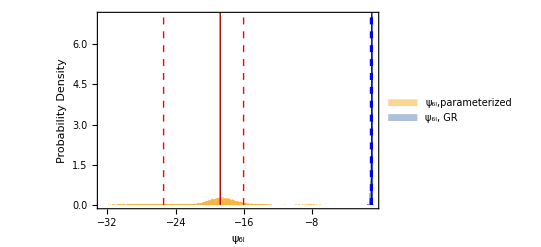

输入Mc范围：{16,33}

输入q范围：{1,7}

m1范围：{18.3792,108.936}

m2范围：{7.54535,37.907}

原始数据量 = 46625，降采样后数据量 = 46625（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在有限先验区间内的积分值S = 0.999999

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.999999 and 8.99198×10^-6 for the integral and error estimates.

归一化后先验区间内积分值 = 0.999999（误差应<1e-5）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{1.×10^-7}

等高线数量：1 条

第一条等高线的前5个边界点：{{41.5516,37.62},{41.6285,37.5694},{42.2628,37.3649},{42.4,37.2859},{43.7812,36.8227}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

===== 第i$201161条等高线 =====

包含闭合区域数：1

区域内总积分值：0.999985

可信水平百分比：99.9985%

==========================

```mathematica
order="6l";
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[{16,33},{1,7}];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.0000001};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[-1]][[2]];
```

```mathematica
prob
```

0.555864

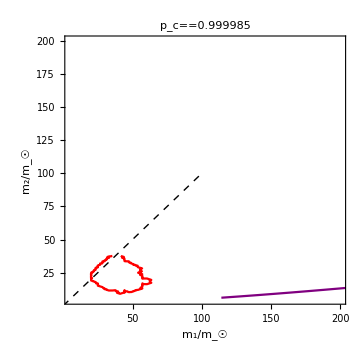

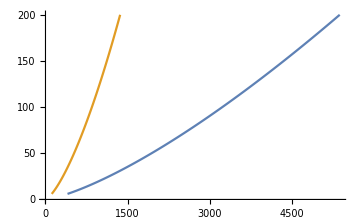

```mathematica
m1s=Range[5,200,1];
m2s=Range[5,200,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],
(*contourPoints[n][[2]],*)

Reverse/@tapes[n][n][[1]][[2;;]],
Reverse/@tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]

ListLinePlot[{Reverse/@tapes[n][n][[1]][[2;;]],Reverse/@tapes[n][n][[2]][[2;;]]}]
```

### 7/2PN

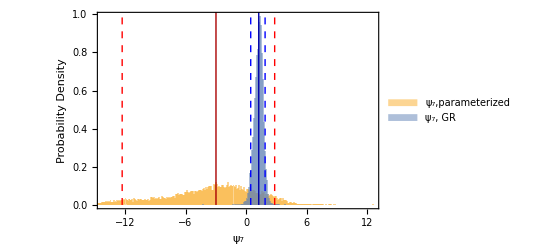

输入Mc范围：{16,33}

输入q范围：{1,7}

m1范围：{18.3792,108.936}

m2范围：{7.54535,37.907}

原始数据量 = 49266，降采样后数据量 = 49266（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在有限先验区间内的积分值S = 0.999995

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 6.41409×10^-6 for the integral and error estimates.

归一化后先验区间内积分值 = 1.（误差应<1e-5）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{0.00365}

等高线数量：1 条

第一条等高线的前5个边界点：{{34.55,16.0103},{33.3151,16.2201},{31.8291,16.3922},{31.3159,16.5585},{30.8205,16.7623}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

===== 第i$226965条等高线 =====

包含闭合区域数：1

区域内总积分值：0.729046

可信水平百分比：72.9046%

==========================

```mathematica
order=7;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[{16,33},{1,7}];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.00365};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];
```

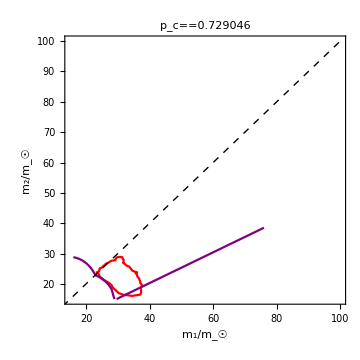

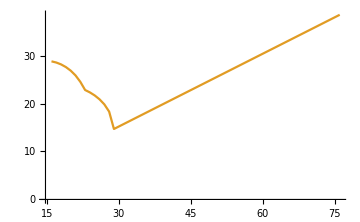

```mathematica
(*prob=0.73*)
m1s=Range[15,100,1];
m2s=Range[15,100,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]

ListLinePlot[{tapes[n][n][[1]][[2;;]],tapes[n][n][[2]][[2;;]]}]
```

```mathematica
tapes[n][n][[1]][[2;;]]
```

{{16,-91.6765+187.157 ⅈ},{17,-95.8529+194.107 ⅈ},{18,-99.9762+200.896 ⅈ},{19,-104.051+207.536 ⅈ},{20,-108.079+214.04 ⅈ},{21,-112.066+220.415 ⅈ},{22,-116.013+226.671 ⅈ},{23,-119.922+232.815 ⅈ},{24,-123.797+238.854 ⅈ},{25,-127.639+244.794 ⅈ},{26,-131.45+250.641 ⅈ},{27,-135.231+256.398 ⅈ},{28,-138.985+262.072 ⅈ},{29,-142.712+267.667 ⅈ},{30,-146.413+273.185 ⅈ},{31,-150.09+278.631 ⅈ},{32,-153.744+284.007 ⅈ},{33,-157.376+289.317 ⅈ},{34,-160.987+294.564 ⅈ},{35,-164.578+299.751 ⅈ},{36,-168.149+304.878 ⅈ},{37,-171.701+309.95 ⅈ},{38,-175.235+314.967 ⅈ},{39,-178.751+319.933 ⅈ},{40,-182.251+324.848 ⅈ},{41,-185.735+329.715 ⅈ},{42,-189.202+334.535 ⅈ},{43,-192.655+339.31 ⅈ},{44,-196.093+344.041 ⅈ},{45,-199.516+348.73 ⅈ},{46,-202.926+353.378 ⅈ},{47,-206.322+357.986 ⅈ},{48,-209.705+362.555 ⅈ},{49,-213.075+367.086 ⅈ},{50,-216.434+371.581 ⅈ},{51,-219.78+376.041 ⅈ},{52,-223.114+380.466 ⅈ},{53,-226.437+384.858 ⅈ},{54,-229.749+389.216 ⅈ},{55,-233.051+393.544 ⅈ},{56,-236.342+397.839 ⅈ},{57,-239.622+402.105 ⅈ},{58,-242.893+406.341 ⅈ},{59,-246.153+410.549 ⅈ},{60,-249.404+414.728 ⅈ},{61,-252.646+418.88 ⅈ},{62,-255.879+423.005 ⅈ},{63,-259.103+427.103 ⅈ},{64,-262.318+431.176 ⅈ},{65,-265.524+435.224 ⅈ},{66,-268.722+439.247 ⅈ},{67,-271.912+443.246 ⅈ},{68,-275.094+447.222 ⅈ},{69,-278.268+451.174 ⅈ},{70,-281.434+455.104 ⅈ},{71,-284.593+459.012 ⅈ},{72,-287.744+462.898 ⅈ},{73,-290.888+466.762 ⅈ},{74,-294.024+470.606 ⅈ},{75,-297.154+474.429 ⅈ},{76,-300.277+478.232 ⅈ},{77,-303.393+482.015 ⅈ},{78,-306.503+485.779 ⅈ},{79,-309.606+489.524 ⅈ},{80,-312.702+493.25 ⅈ},{81,-315.792+496.958 ⅈ},{82,-318.876+500.647 ⅈ},{83,-321.954+504.319 ⅈ},{84,-325.026+507.973 ⅈ},{85,-328.092+511.61 ⅈ},{86,-331.152+515.23 ⅈ},{87,-334.206+518.834 ⅈ},{88,-337.255+522.421 ⅈ},{89,-340.298+525.992 ⅈ},{90,-343.336+529.547 ⅈ},{91,-346.368+533.086 ⅈ},{92,-349.395+536.61 ⅈ},{93,-352.417+540.119 ⅈ},{94,-355.434+543.613 ⅈ},{95,-358.445+547.093 ⅈ},{96,-361.452+550.557 ⅈ},{97,-364.453+554.008 ⅈ},{98,-367.45+557.444 ⅈ},{99,-370.442+560.867 ⅈ},{100,-373.429+564.275 ⅈ}}

Part::partw: Part 7 of … does not exist.

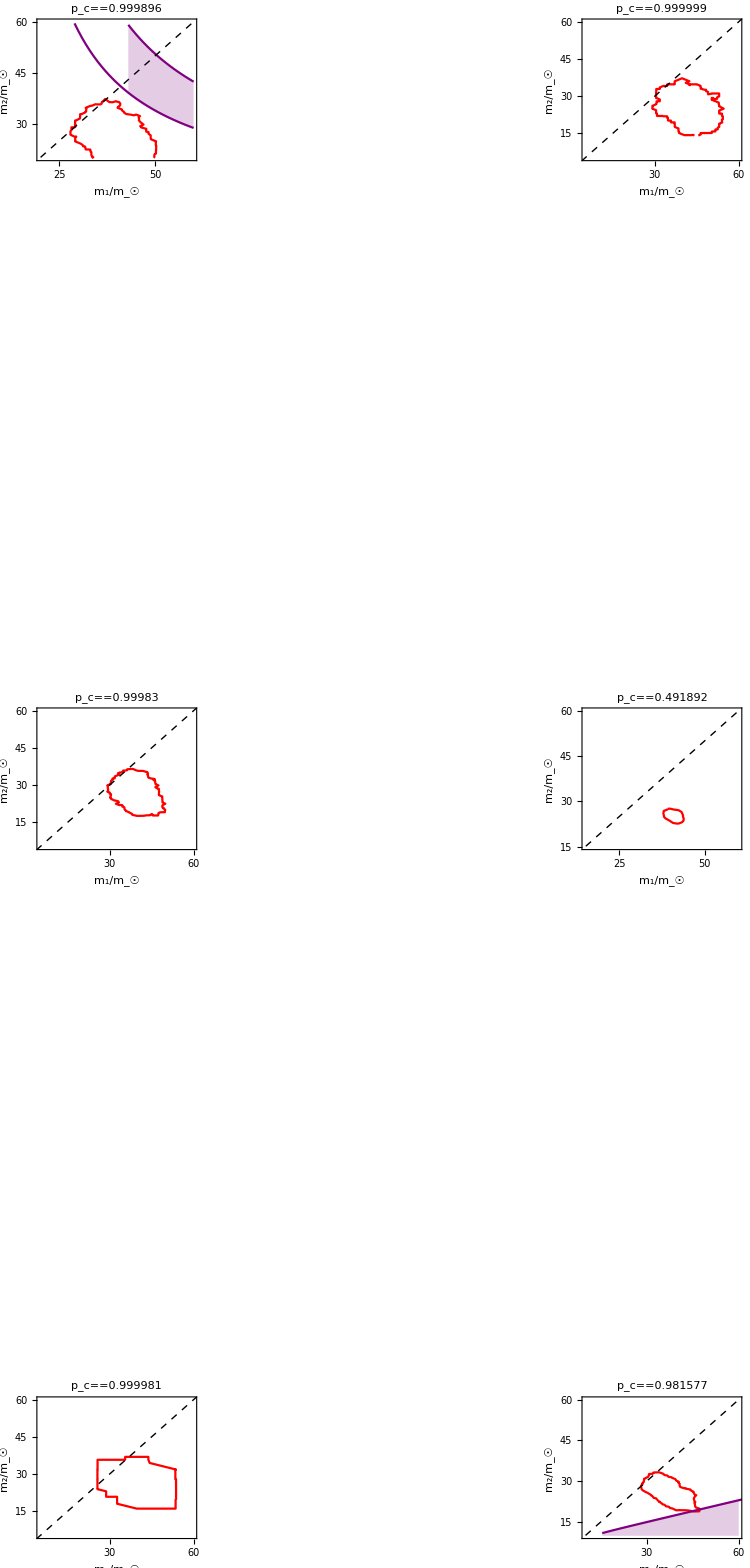

```mathematica
combinedPlot=GraphicsGrid[
Append[Partition[Values[plots],2],{plots[[7]],}],(*将1维数组拆分为3×3的二维网格*)
(*Frame->All,*)(*给每个子图加边框，清晰分隔*)
(*Spacings->{15,15},*)(*控制子图间的水平/垂直间距（像素）*)
ImageSize->750,(*控制整个大图的总尺寸*)
PlotLabel->Style["3×3组合大图",16,Bold]  (*给整个大图加总标题*)]
```

## (old) m1-m2 Plot, 22

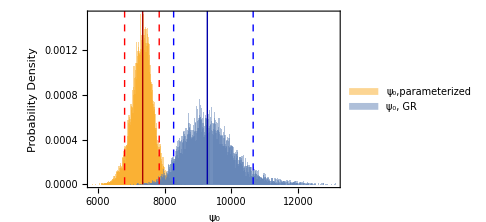

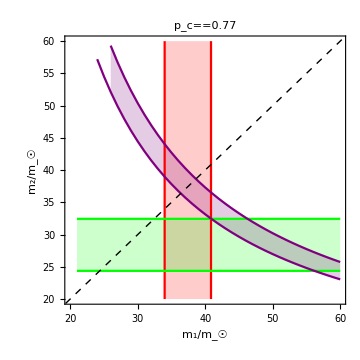

```mathematica
m1s=Range[20,60,1];
m2s=Range[20,60,1];

order=0;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]

prob=0.77;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

Select[tapes[n][n][[1]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]],
Select[tapes[n][n][[2]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Filling->{1->{2},3->{4},5->{6}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

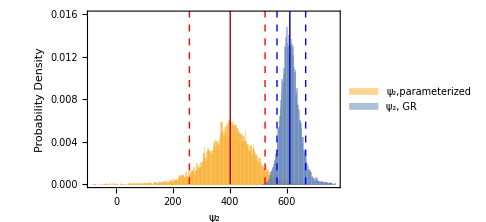

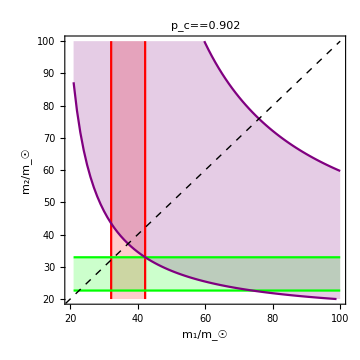

```mathematica
m1s=Range[20,100,1];
m2s=Range[20,100,1];

order=2;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]

prob=0.902;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{2,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]
(*Select[tapes[n][n][[2]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]]*)};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,2]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

```mathematica
1-0.902^3
```

0.266129

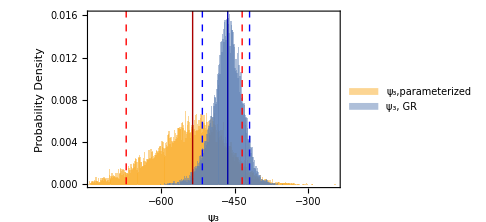

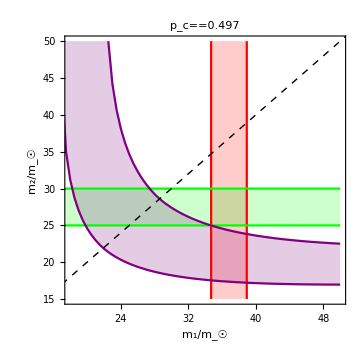

```mathematica
m1s=Range[15,50,1/2];
m2s=Range[15,50,1/2];

order=3;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]


prob=0.497;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{3,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,3]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,PlotRange->{{18,m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],
Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

```mathematica
1-0.495^3
```

0.878713

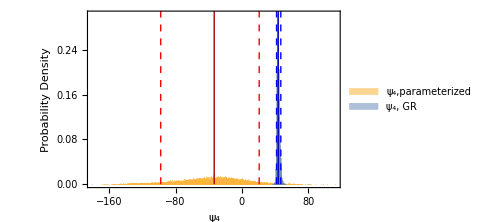

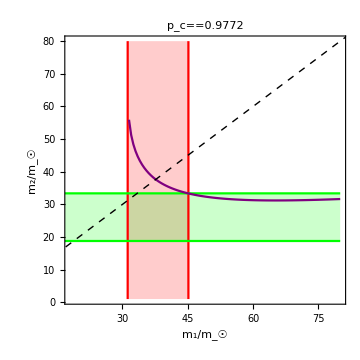

```mathematica
m1s=Range[1,80,1/2];
m2s=Range[1,80,1/2];

order=4;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]


prob=0.9772;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{4,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,PlotRange->{{18,m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],
Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

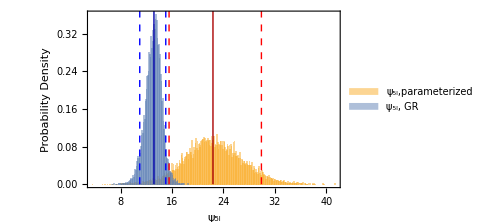

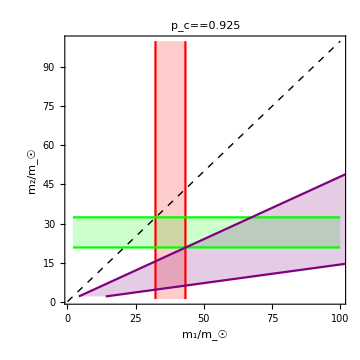

```mathematica
m1s=Range[1,100,1];
m2s=Range[1,100,1];

order="5l";
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]


prob=0.9250;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

Reverse/@tapes[n][n][[1]][[2;;]],
Reverse/@tapes[n][n][[2]][[2;;]],
{(Reverse/@tapes[n][n][[1]][[2;;]])[[1]],(Reverse/@tapes[n][n][[2]][[2;;]])[[1]]}(* 补上紫线左边的阴影区 *)
};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,"5l"]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],

PlotStyle->{Red,Red,Green,Green,Purple,Purple,Transparent},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6},5->{7}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

```mathematica
BCI[n][n]
```

{15.535,22.3649,29.9001}

```mathematica
1-0.925^3
```

0.208547

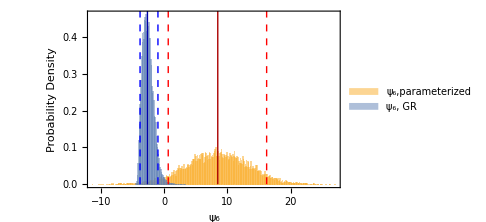

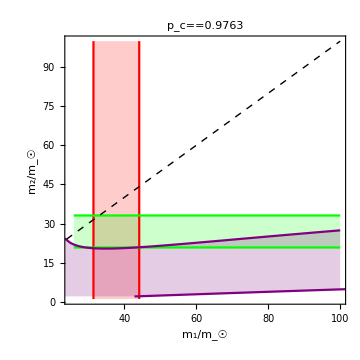

```mathematica
m1s=Range[25,100,1];
m2s=Range[1,100,1];

order=6;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]

prob=0.9763;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

tapes[n][n][[1]][[2;;]],
Reverse/@tapes[n][n][[2]][[2;;]],
{(Reverse/@tapes[n][n][[1]][[2;;]])[[1]],(Reverse/@tapes[n][n][[2]][[2;;]])[[1]]}(* 补上紫线左边的阴影区 *)
};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],

PlotStyle->{Red,Red,Green,Green,Purple,Purple,Transparent},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6},5->{7}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

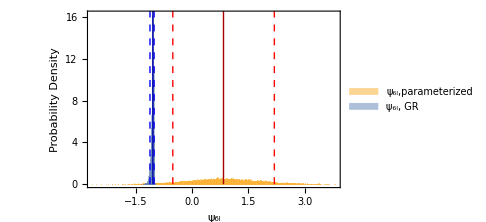

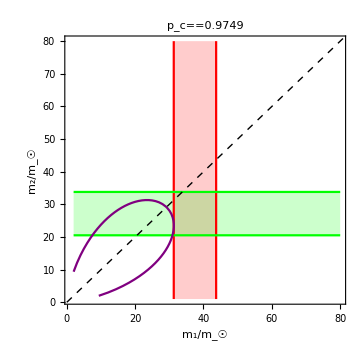

```mathematica
m1s=Range[1,80,1];
m2s=Range[1,80,1];

order="6l";
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]


prob=0.9749;
(*prob=0.9891;*)

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

Join[Reverse/@Select[Reverse/@tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&],Reverse[Select[Reverse/@tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]]],
Reverse/@tapes[n][n][[2]][[2;;]],
{(Reverse/@tapes[n][n][[1]][[2;;]])[[1]],(Reverse/@tapes[n][n][[2]][[2;;]])[[1]]}(* 补上紫线左边的阴影区 *)
};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],

PlotStyle->{Red,Red,Green,Green,Purple,Purple,Transparent},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6},5->{7}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

```mathematica
combinedPlot=GraphicsGrid[
Append[Partition[Values[plots],2],{plots[[7]],}],(*将1维数组拆分为3×3的二维网格*)
(*Frame->All,*)(*给每个子图加边框，清晰分隔*)
(*Spacings->{15,15},*)(*控制子图间的水平/垂直间距（像素）*)
ImageSize->750,(*控制整个大图的总尺寸*)
PlotLabel->Style["3×3组合大图",16,Bold]  (*给整个大图加总标题*)]
```

Part::partw: Part 7 of … does not exist.

-Graphics-

## Value Domains

```mathematica
vd=<||>;
```

```mathematica
(BCI["cpsi0"]["cpsi0"][[3]]-BCI["cpsi0"]["cpsi0"][[1]])/5000
vd["cpsi0"]=Manipulate[
Plot3D[
Function[{m1,m2},Psi[0,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi0"]["mass1"][[1]],BCI["cpsi0"]["mass1"][[3]]},
{m2,BCI["cpsi0"]["mass2"][[1]],BCI["cpsi0"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False,
AxesLabel->{TraditionalForm[Subscript[m,1]/Subscript[m,"☉"]],TraditionalForm[Subscript[m,2]/Subscript[m,"☉"]],TraditionalForm[Subscript[ψ,order]]}
],
{spin1z,BCI["cpsi0"]["spin1z"][[2]]},{spin2z,BCI["cpsi0"]["spin2z"][[2]]}
]
```

0.206569

```mathematica
(BCI["cpsi2"]["cpsi2"][[3]]-BCI["cpsi2"]["cpsi2"][[1]])/250
vd["cpsi0"]=Manipulate[
Plot3D[
Function[{m1,m2},Psi[2,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi2"]["mass1"][[1]],BCI["cpsi2"]["mass1"][[3]]},
{m2,BCI["cpsi2"]["mass2"][[1]],BCI["cpsi2"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi2"]["spin1z"][[2]]},{spin2z,BCI["cpsi2"]["spin2z"][[2]]}
]
```

1.06474

```mathematica
(BCI["cpsi3"]["cpsi3"][[3]]-BCI["cpsi3"]["cpsi3"][[1]])/150
Manipulate[
Plot3D[
Function[{m1,m2},Psi[3,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi3"]["mass1"][[1]],BCI["cpsi3"]["mass1"][[3]]},
{m2,BCI["cpsi3"]["mass2"][[1]],BCI["cpsi3"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi3"]["spin1z"][[2]]},{spin2z,BCI["cpsi3"]["spin2z"][[2]]}
]
```

1.57419

Part::partw: Part 3 of Missing[KeyAbsent,cpsi3][mass1] does not exist.

Plot3D::plln: Limiting value mass1 in {m1,mass1,Missing[KeyAbsent,cpsi3][mass1]⟦3⟧} is not a machine-sized real number.

Part::partw: Part 3 of Missing[KeyAbsent,cpsi3][mass1] does not exist.

Plot3D::plln: Limiting value mass1 in {m1,mass1,Missing[KeyAbsent,cpsi3][mass1]⟦3⟧} is not a machine-sized real number.

```mathematica
(BCI["cpsi4"]["cpsi4"][[3]]-BCI["cpsi4"]["cpsi4"][[1]])/5
Manipulate[
Plot3D[
Function[{m1,m2},Psi[4,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi4"]["mass1"][[1]],BCI["cpsi4"]["mass1"][[3]]},
{m2,BCI["cpsi4"]["mass2"][[1]],BCI["cpsi4"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi4"]["spin1z"][[2]]},{spin2z,BCI["cpsi4"]["spin2z"][[2]]}
]
```

23.7613

```mathematica
(BCI["cpsi5l"]["cpsi5l"][[3]]-BCI["cpsi5l"]["cpsi5l"][[1]])/1.5
Manipulate[
Plot3D[
Function[{m1,m2},Psi["5l",η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi5l"]["mass1"][[1]],BCI["cpsi5l"]["mass1"][[3]]},
{m2,BCI["cpsi5l"]["mass2"][[1]],BCI["cpsi5l"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi5l"]["spin1z"][[2]]},{spin2z,BCI["cpsi5l"]["spin2z"][[2]]}
]
```

9.56092

```mathematica
Manipulate[
Plot3D[
Function[{m1,m2},Psi["5l",η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,3,100},
{m2,3,100},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi5l"]["spin1z"][[2]]},{spin2z,BCI["cpsi5l"]["spin2z"][[2]]}
]
```

```mathematica
(BCI["cpsi6"]["cpsi6"][[3]]-BCI["cpsi6"]["cpsi6"][[1]])/0.5
Manipulate[
Plot3D[
Function[{m1,m2},Psi[6,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi6"]["mass1"][[1]],BCI["cpsi6"]["mass1"][[3]]},
{m2,BCI["cpsi6"]["mass2"][[1]],BCI["cpsi6"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi6"]["spin1z"][[2]]},{spin2z,BCI["cpsi6"]["spin2z"][[2]]}
]
```

31.1398

```mathematica
(BCI["cpsi6l"]["cpsi6l"][[3]]-BCI["cpsi6l"]["cpsi6l"][[1]])/0.1
Manipulate[
Plot3D[
Function[{m1,m2},Psi["6l",η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi6l"]["mass1"][[1]],BCI["cpsi6l"]["mass1"][[3]]},
{m2,BCI["cpsi6l"]["mass2"][[1]],BCI["cpsi6l"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi6l"]["spin1z"][[2]]},{spin2z,BCI["cpsi6l"]["spin2z"][[2]]}
]
```

27.0383

```mathematica
(*Manipulate[
Plot3D[
Function[{m1,m2},Psi[7,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,20,80},
{m2,20,80},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,0.06070798549182338},{spin2z,0.09392835788044217}
(*{spin1z,-1,1},{spin2z,-1,1}*)
]*)
```

## Exports

```mathematica
Do[
name=deviationNames[[i]];
exportPath=StringJoin["D:/Documents/workspace/课题/论文/figs/GW150914/comp_plots/","GW150914_inverse_plot_",
name,
".pdf"];
Export[exportPath,compPlots[name],"PDF",ImageResolution->1000],
{i,1,Length[deviationNames]}]
```

```mathematica
Do[
name=deviationNames[[i]];
exportPath=StringJoin["D:/Documents/workspace/课题/论文/figs/GW150914/inverse_plots/","GW150914_inverse_plot_",
name,
".pdf"];
Export[exportPath,plots[name],"PDF",ImageResolution->1000],
{i,1,Length[deviationNames]}]
```

```mathematica
Export["D:/Documents/workspace/课题/论文/figs/GW150914/inverse_plots/GW150914_patch_cpsi6.pdf",patch6,"PDF",ImageResolution->1000]
```

D:/Documents/workspace/课题/论文/figs/GW150914/inverse_plots/GW150914_patch_cpsi6.pdf

```mathematica
Do[
name=deviationNames[[i]];
exportPath=StringJoin["D:/Documents/workspace/课题/论文/figs/GW150914/value_domains/","GW150914_vd_",
name,
".pdf"];
Export[exportPath,vd[name],"PDF",ImageResolution->1000],
{i,1,Length[deviationNames]}]
```

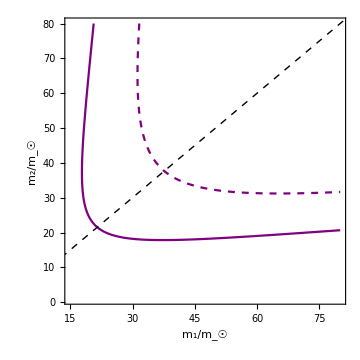

```mathematica
m1s=Range[15,80,1];
m2s=Range[1,80,1];

order=4;
n="cpsi"<>ToString[order];

prob1=0.9772;
(*再大一点会扫过这个矩形*)
prob2=0.989;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];
pInterval[n]=Join[IntervalFromProbability[prob2],IntervalFromProbability[prob1]];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m1s},{2},
{4,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
Join[Reverse[Reverse/@Select[tapes[n][n][[2]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[2]][[2;;]],#[[1]]>=#[[2]]&]],
Join[Reverse[Reverse/@Select[tapes[n][n][[4]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[4]][[2;;]],#[[1]]>=#[[2]]&]]
(*tapes[n][n][[2]][[2;;]],
tapes[n][n][[4]][[2;;]]*)
};
legends[n]=Panel[
Column[{
LineLegend[{Directive[Purple,Dashed],Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[ψ,4],", ",With[{value=prob1},TraditionalForm[HoldForm[p==value]]]}]],
TraditionalForm[Row[{Subscript[ψ,4],", ",With[{value=prob2},TraditionalForm[HoldForm[p==value]]]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left](*,
Background->White*)
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{
Purple,
Directive[Purple,Dashed]
},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{
(*1->{2},3->{4},*)
(*6->{7},8->{9},*)
5->{10}},
FillingStyle->{HatchFilling["Diagonal"]},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],1m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Black,Dashed,Line[{{0,0},{100,100}}],
Inset[
legends[n],
Scaled[{0.3,0.8}],
{0,0}
]
},
(*PlotLabel->With[{value=prob},TraditionalForm[HoldForm[p==value]]],*)
ImageSize->Medium]
```

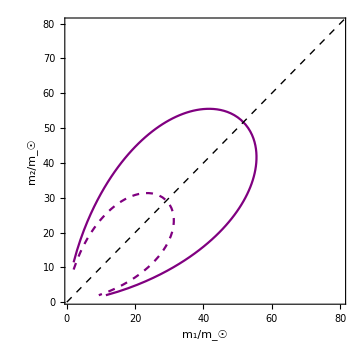

```mathematica
m1s=Range[1,80,1];
m2s=Range[1,80,1];

order="6l";
n="cpsi"<>ToString[order];

prob1=0.9749;
prob2=0.9891;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];
pInterval[n]=Join[IntervalFromProbability[prob2],IntervalFromProbability[prob1]];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m1s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[Reverse[Reverse/@Select[tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]],
Join[Reverse[Reverse/@Select[tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&]]*)
Join[Reverse/@Select[Reverse/@tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&],Reverse[Select[Reverse/@tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]]],
Join[Reverse/@Select[Reverse/@tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&],Reverse[Select[Reverse/@tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&]]]
};
legends[n]=Panel[
Column[{
LineLegend[{Directive[Purple,Dashed],Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[ψ,order],", ",With[{value=prob1},TraditionalForm[HoldForm[p==value]]]}]],
TraditionalForm[Row[{Subscript[ψ,order],", ",With[{value=prob2},TraditionalForm[HoldForm[p==value]]]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left](*,
Background->White*)
];

patch6=ListLinePlot[
{
(*Join[Reverse[Reverse/@Select[tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]],
Join[Reverse[Reverse/@Select[tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&]]*)
tapes[n][n][[1]][[2;;]],
tapes[n][n][[3]][[2;;]]
},
PlotStyle->{
Purple,
Directive[Purple,Dashed]
},

Filling->{
(*1->{2},3->{4},*)
(*6->{7},8->{9},*)
5->{10}},
FillingStyle->{HatchFilling["Diagonal"]},
AspectRatio->1,
PlotRange->{{40.02,40.026},{30.015,30.020}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Black,Dashed,Line[{{0,0},{100,100}}]
},
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
(*PlotLabel->With[{value=prob},TraditionalForm[HoldForm[p==value]]],*)
ImageSize->Medium];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{
Purple,
Directive[Purple,Dashed]
},

Axes->True,
Frame->True,
FrameTicks->True,
Filling->{
(*1->{2},3->{4},*)
(*6->{7},8->{9},*)
5->{10}},
FillingStyle->{HatchFilling["Diagonal"]},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],1m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],
Scaled[{0.3,0.8}],
{0,0}
],
Black,Dashed,Line[{{0,0},{100,100}}](*,
Inset[
patch6]*)
},
(*PlotLabel->With[{value=prob},TraditionalForm[HoldForm[p==value]]],*)
ImageSize->Medium]
```

```mathematica
name="cpsi6l";
exportPath=StringJoin["D:/Documents/workspace/课题/论文/figs/GW150914/inverse_plots/","GW150914_inverse_plot_",
name,
"_double",
".pdf"];
Export[exportPath,plots[name],"PDF",ImageResolution->1000]
```

D:/Documents/workspace/课题/论文/figs/GW150914/inverse_plots/GW150914_inverse_plot_cpsi6l_double.pdf